```mathematica
everest=Entity["Mountain","MountEverest"]
```

Mount Everest

```mathematica
region=GeoBoundingBox[everest,Quantity[30,"Kilometers"]]
```

{GeoPosition[{27.7174,86.6203}],GeoPosition[{28.2588,87.2303}]}

```mathematica
elevData=GeoElevationData[region,GeoRange->Quantity[4, "Kilometers"],GeoProjection->Automatic]
```

QuantityArray[…]

```mathematica
map=ListContourPlot[
elevData,
DataRange->All,
Contours->25,
Frame->True,
ColorFunction->Function[{f},RGBColor["#1e1e2e"]],
ContourStyle->DarkGray,
FrameTicks->All,
Axes->None,
ImagePadding->0
]
```

```mathematica
Export[NotebookDirectory[]<>"bgd.png",Rasterize[map,ImageResolution->300]]
```

D:\11\website\resources\bgd.png

```mathematica
<<Taggar`MGroups`
```

```mathematica
Subscript[S, 5]=MPermutationsGroup[5];
```

```mathematica
subs=MSubgroups[Subscript[S, 5],MCombinationsLimit->2][[1]][[All,1]];
```

```mathematica
rel=Select[Tuples[subs,2],SubsetQ@@#&];
```

```mathematica
g=Graph[Rule@@@rel,DirectedEdges->True];
```

```mathematica
paths=SortBy[
FindPath[Rule@@@rel,Sort@MGroupDomain[Subscript[S, 5]],{"(1)"},Infinity,All],
Length];
```

```mathematica
paths=SortBy[paths,Length];
```

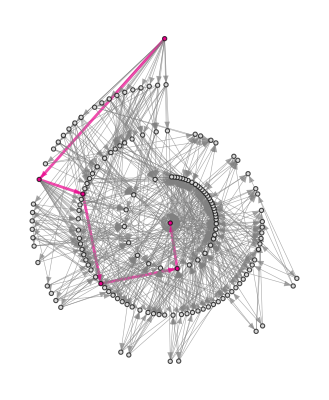

```mathematica
g=TransitiveReductionGraph[
Rule@@@rel,
GraphLayout->"RadialEmbedding",
VertexSize->1.5,
VertexStyle->(#->If[MemberQ[paths[[-1]],#],RGBColor["#EB008B"],LightGray]&/@subs),
EdgeStyle->(#->If[MemberQ[DirectedEdge@@@Partition[paths[[-1]],2,1],#],Directive[RGBColor["#EB008B"],Thickness[0.005]],Directive[Gray,Thickness[0.001]]]&/@(DirectedEdge@@@rel)),
BaseStyle->Arrowheads[0.02]
]
```

```mathematica
Export[NotebookDirectory[]<>"s5g.svg",%]
```

D:\11\website\resources\s5g.svg